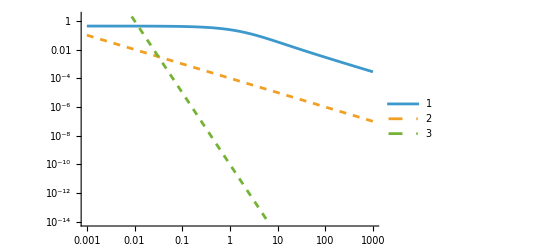

```mathematica
θ = 5;
n = 2;
LogLogPlot[{
Exp[-10(1./(k+1.))]Sum[(m/(m+θ))^n(10(1./(k + 1.)))^m/Factorial[m], {m, 1, 150}]
, 10^-4 k^-1 
,10^-10 k^-θ
},{k, 0.001,1000},
PlotLegends->Automatic, PlotRange->{Automatic,{10^-14, 2*10^0}}, PlotStyle->{{Solid}, Dashed, Dashed}]
```

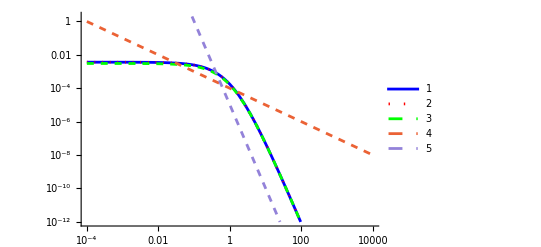

```mathematica
θ = 5;
LogLogPlot[{
1-Exp[-(1./(k+1.))]*Sum[(1./(k + 1.))^m/Factorial[m], {m, 0, θ-1}]
,Exp[-(1./(k+1.))]*Sum[(1./(k + 1.))^m/Factorial[m], {m, θ,2θ}]
,Exp[-(1./(k+1.))]*(1./(k + 1.))^θ/Factorial[θ]
, 10^-4 k^-1 
,10^-5 k^-θ
},{k, 0.0001,10000},
PlotLegends->Automatic, PlotRange->{Automatic,{10^-12, 2*10^0}}, PlotStyle->{{Solid, Blue}, {Dotted, Red}, {Dashed, Green}, Dashed, Dashed}]
```

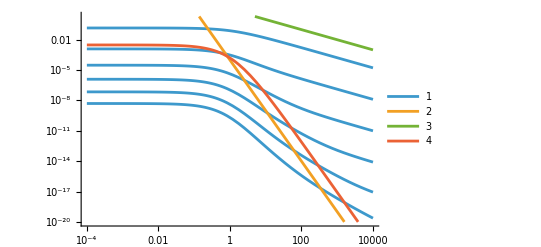

```mathematica
θ = 5;
Subscript[θ, c] = (Factorial[θ]/θ^5)^(1/(θ-1));
LogLogPlot[{Table[{Exp[-10^0(1./(k+1.))]Sum[(m/(m+θ))^(4*n + 1)((10^0(1./(k + 1.)))^m)/Factorial[m], {m, 0, 100}]}, {n, 0, 5}]
,10^-4 k^-θ
,10 k^-1
,Exp[-(1./(k+1.))]*(1./(k + 1.))^θ/Factorial[θ]
},{k, 0.0001,10000},
PlotLegends->Automatic
,PlotRange->{Automatic,{10^-20, 2*10^0}}]
```

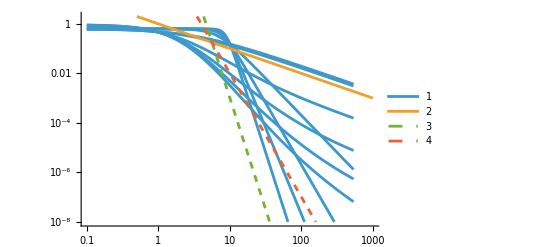

```mathematica
θ = 5;
(*n = 5;*)
LogLogPlot[{Table[{
1-Exp[-(((10 k^-1)^(2*n+1))/((10 k^-1)^(2*n+1)+θ))]
,Exp[-10(1./(k+1.))]Sum[(m^(2*n+1)/(m^(2*n+1)+θ^(2*n+1)))(10(1./(k + 1.)))^m/Factorial[m], {m, 1, 20}]}, {n, 0, 4}]
, 1 k^-1 
, 1000000 k^-9 
,1000 k^-θ
},{k, 0.1,1000},
PlotLegends->Automatic, PlotRange->{Automatic,{10^-8, 2*10^0}}, PlotStyle->{{Solid},{Solid}, Dashed, Dashed, Dashed}]
```

```mathematica
pi(E_) = 
(*Continuous model*)
```